```mathematica
Convolve[HeavisideTheta[t],t^2*HeavisideTheta[t],t,x]
```

1/3 x^3 HeavisideTheta[x]

```mathematica
D[(3-t)*(HeavisideTheta[t]-HeavisideTheta[t-2]),t]
```

(3-t) (-DiracDelta[-2+t]+DiracDelta[t])+HeavisideTheta[-2+t]-HeavisideTheta[t]

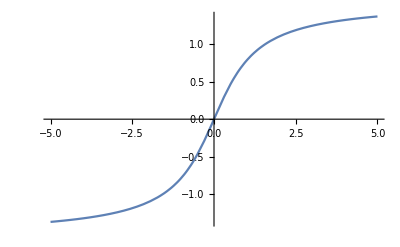

```mathematica
Plot[ArcTan[x],{x,-5,5}]
```

```mathematica
D[ArcTan[x],x]
```

1/(1+x^2)

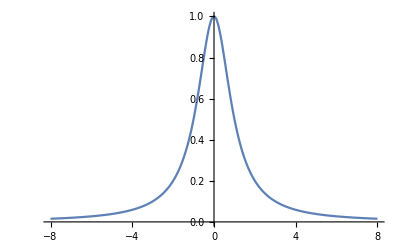

```mathematica
Plot[1/(1+x^2),{x,-8,8}]
```

```mathematica
D[Sin[1/x],x]
```

-Cos[1/x]/x^2

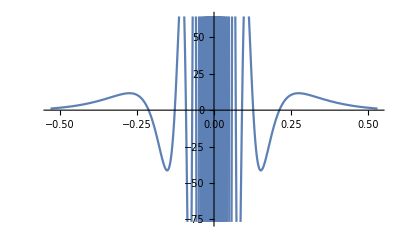

```mathematica
Plot[-Cos[1/x]/x^2,{x,-0.5305164769729844,0.5305164769729844}]
```

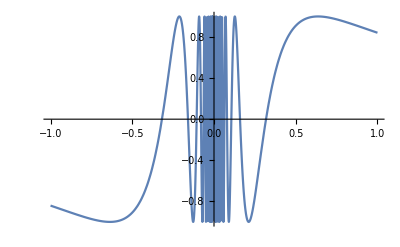

```mathematica
Plot[Sin[1/x],{x,-1,1}]
```

```mathematica
D[Exp[-x]*Sin[1/x],x]
```

-(ⅇ^-x Cos[1/x])/x^2-ⅇ^-x Sin[1/x]

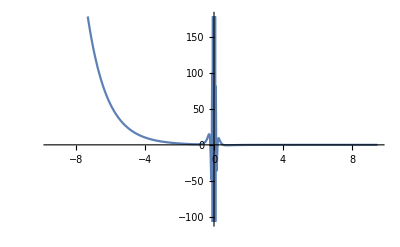

```mathematica
Plot[-(ⅇ^-x Cos[1/x])/x^2-ⅇ^-x Sin[1/x],{x,-9.477464829275686,9.477464829275686}]
```

```mathematica
Limit[-(ⅇ^-x Cos[1/x])/x^2-ⅇ^-x Sin[1/x],x->-Infinity]
```

∞

```mathematica
Integrate[Tan[x],x]
```

-Log[Cos[x]]

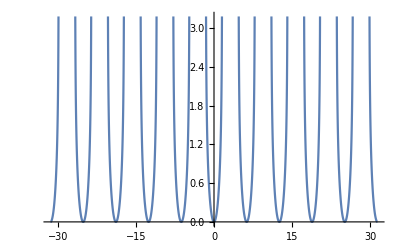

```mathematica
Plot[-Log[Cos[x]],{x,-10 π,10 π}]
```

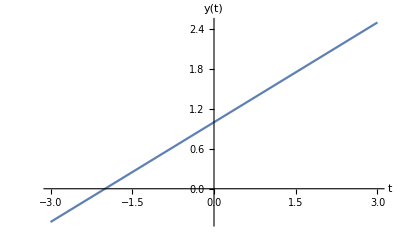

```mathematica
Plot[1/2*x+1,{x,-3,3},AxesLabel->{t,"y(t)"}]
```

```mathematica
Export["D:\\Documents\\Sophomore\\VE216,Intro to Signals and Systems\\Homework_2\\5(b).eps",%26,"EPS"]
```

D:\Documents\Sophomore\VE216,Intro to Signals and Systems\Homework_2\5(b).eps

```mathematica
Convolve[(1-Abs[t/2])*(HeavisideTheta[t+2]-HeavisideTheta[t-2]),HeavisideTheta[t]-HeavisideTheta[t-2],t,x]
```

1/4 (-(-4+x)^2 HeavisideTheta[-4+x]+2 (-2+x)^2 HeavisideTheta[-2+x]-x^2 HeavisideTheta[x])+1/4 ((-2+x)^2 HeavisideTheta[-2+x]-2 x^2 HeavisideTheta[x]+(2+x)^2 HeavisideTheta[2+x])

```mathematica
Simplify[1/4 (-(-4+x)^2 HeavisideTheta[-4+x]+2 (-2+x)^2 HeavisideTheta[-2+x]-x^2 HeavisideTheta[x])+1/4 ((-2+x)^2 HeavisideTheta[-2+x]-2 x^2 HeavisideTheta[x]+(2+x)^2 HeavisideTheta[2+x])]
```

1/4 (-(-4+x)^2 HeavisideTheta[-4+x]+3 (-2+x)^2 HeavisideTheta[-2+x]-3 x^2 HeavisideTheta[x]+(2+x)^2 HeavisideTheta[2+x])

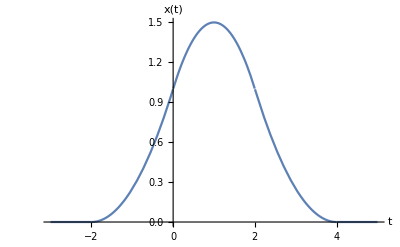

```mathematica
Plot[1/4 (-(-4+x)^2 HeavisideTheta[-4+x]+3 (-2+x)^2 HeavisideTheta[-2+x]-3 x^2 HeavisideTheta[x]+(2+x)^2 HeavisideTheta[2+x]),{x,-3,5},AxesLabel->{t,"x(t)"}]
```

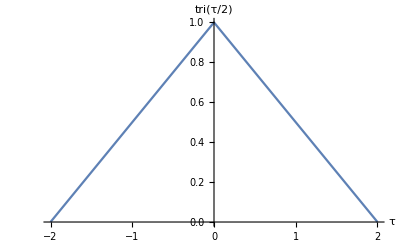

```mathematica
Plot[(1-Abs[t/2])*(HeavisideTheta[t+2]-HeavisideTheta[t-2]),{t,-2,2},AxesLabel->{"τ","tri(τ/2)"}]
```

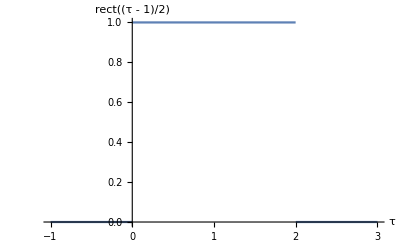

```mathematica
Plot[HeavisideTheta[t]-HeavisideTheta[t-2],{t,-1,3},AxesLabel->{"τ","rect((τ - 1)/2)"}]
```

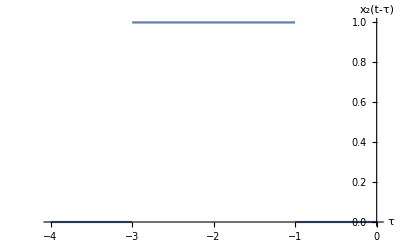

```mathematica
Plot[HeavisideTheta[-t-1]-HeavisideTheta[-t-3],{t,-4,0},AxesLabel->{"τ","x_2(t-τ)"}]
```

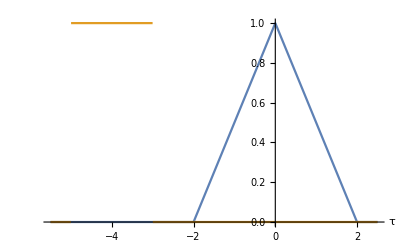

```mathematica
Plot[{(1-Abs[t/2])*(HeavisideTheta[t+2]-HeavisideTheta[t-2]),HeavisideTheta[-t-3]-HeavisideTheta[-t-5]},{t,-5.5,2.5},AxesLabel->{"τ",None},PlotLabels->Placed[{"x_1(τ)","x_2(t-τ)"},Above]]
```

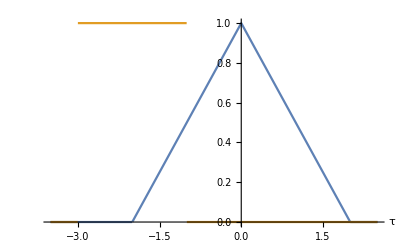

```mathematica
Plot[{(1-Abs[t/2])*(HeavisideTheta[t+2]-HeavisideTheta[t-2]),HeavisideTheta[-t-1]-HeavisideTheta[-t-3]},{t,-3.5,2.5},AxesLabel->{"τ",None},PlotLabels->Placed[{"x_1(τ)","x_2(t-τ)"},Above]]
```

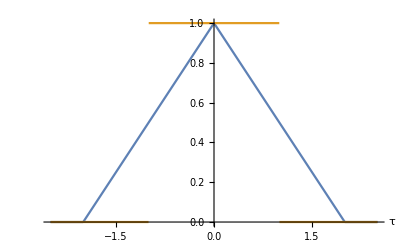

```mathematica
Plot[{(1-Abs[t/2])*(HeavisideTheta[t+2]-HeavisideTheta[t-2]),HeavisideTheta[-t+1]-HeavisideTheta[-t-1]},{t,-2.5,2.5},AxesLabel->{"τ",None},PlotLabels->Placed[{"x_1(τ)","x_2(t-τ)"},Above]]
```

```mathematica
Plot[{(1-Abs[t/2])*(HeavisideTheta[t+2]-HeavisideTheta[t-2]),HeavisideTheta[-t+3]-HeavisideTheta[-t+1]},{t,-2.5,3.5},AxesLabel->{"τ",None},PlotLabels->{Callout["x_1(τ)",{Scaled[0.5],Above}],Callout["x_2(t-τ)",{Scaled[0.75],Above}]}]
```

-Graphics-

```mathematica
Plot[{(1-Abs[t/2])*(HeavisideTheta[t+2]-HeavisideTheta[t-2]),HeavisideTheta[-t+5]-HeavisideTheta[-t+3]},{t,-2.5,5.5},AxesLabel->{"τ",None},PlotLabels->{Callout["x_1(τ)",{Scaled[0.5],Above}],Callout["x_2(t-τ)",{Scaled[0.75],Above}]}]
```

-Graphics-

```mathematica
f[x_]:=If[x≤0,0,If[x<2,0.5*x,1]]
```

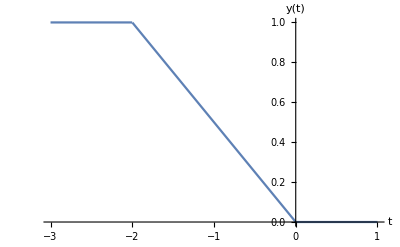

```mathematica
Plot[f[-x],{x,-3,1},AxesLabel->{t,"y(t)"}]
```

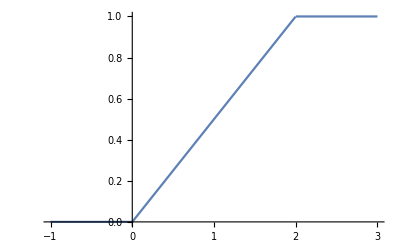

```mathematica
Plot[0.5*t*HeavisideTheta[t]-0.5*(t-2)*HeavisideTheta[t-2],{t,-1,3}]
```

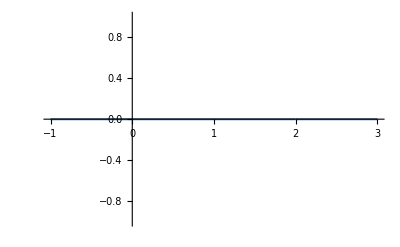

```mathematica
Plot[0.5*DiracDelta[t]-0.5*DiracDelta[t-2],{t,-1,3}]
```

```mathematica
ArrowsDeltaFunction[eqn_,x_]:=Module[{xsubs,listDeltas,coefDeltas,locationDeltas},xsubs=(x/.Cases[eqn,DiracDelta[a__]:>Solve[a==0,x],Infinity])/.x->{};
listDeltas=DiracDelta[x-x0]/.x0->xsubs;
coefDeltas=Flatten[Coefficient[eqn,listDeltas]];
locationDeltas=Flatten[xsubs];
Arrow[Table[{{locationDeltas[[i]],0},{locationDeltas[[i]],coefDeltas[[i]]}},{i,1,Length[locationDeltas]}]]]
```

```mathematica
f:=0.5*DiracDelta[t]-0.5*DiracDelta[t-2]
```

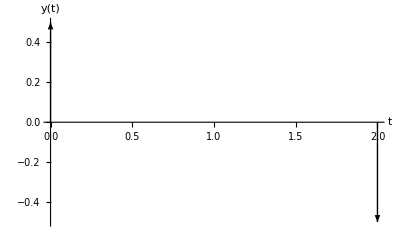

```mathematica
Plot[f,{x,-1,3},Epilog->{ArrowsDeltaFunction[f,t]},AxesLabel->{t,"y(t)"}]
```

```mathematica
Convolve[HeavisideTheta[t-1]-HeavisideTheta[t-3],HeavisideTheta[t+5]-HeavisideTheta[t+1],t,x]
```

(-2+x) HeavisideTheta[-2+x]-x HeavisideTheta[x]-(2+x) HeavisideTheta[2+x]+(4+x) HeavisideTheta[4+x]

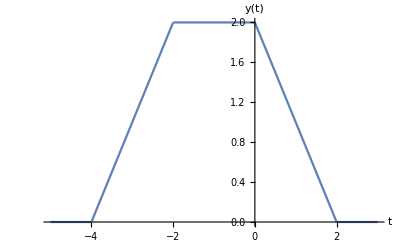

```mathematica
Plot[(-2+x) HeavisideTheta[-2+x]-x HeavisideTheta[x]-(2+x) HeavisideTheta[2+x]+(4+x) HeavisideTheta[4+x],{x,-5,3},AxesLabel->{t,"y(t)"}]
```

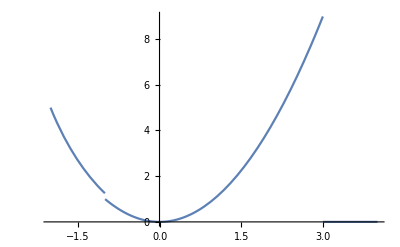

```mathematica
Plot[t^2*(HeavisideTheta[t+3]-HeavisideTheta[t-3])+(t+3)^-2*HeavisideTheta[-t-1],{t,-2,4}]
```

```mathematica
Plot[Integrate[τ^2*x(t-τ),{τ,-3,3}]+Integrate[(t-τ+3)^-2*x(τ),{τ,-Infinity,t+1}],{t,-5,5}]
```

```mathematica
Integrate[DiracDelta[τ],{τ,-Infinity,2}]
```

1

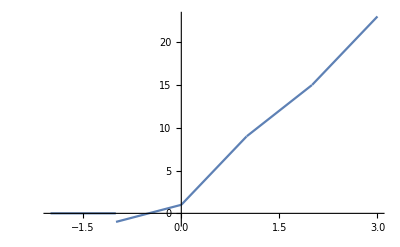

```mathematica
Plot[(2*t+1)*HeavisideTheta[t+1]+6*t*HeavisideTheta[t]+(2-2*t)*HeavisideTheta[t-1]-(4-2*t)*HeavisideTheta[t-2],{t,-2,3}]
```

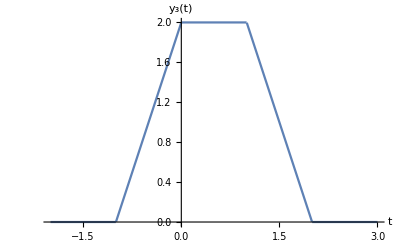

```mathematica
Plot[2*(1-Abs[t])*(HeavisideTheta[t+1]-HeavisideTheta[t-1])+2*(1-Abs[t-1])*(HeavisideTheta[t]-HeavisideTheta[t-2]),{t,-2,3},AxesLabel->{t,"y_3(t)"}]
```

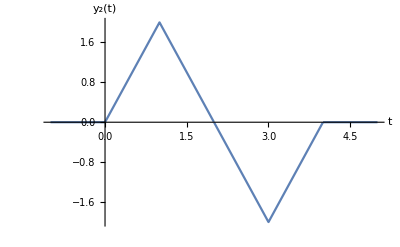

```mathematica
Plot[2*(1-Abs[t-1])*(HeavisideTheta[t]-HeavisideTheta[t-2])-2*(1-Abs[t-3])*(HeavisideTheta[t-2]-HeavisideTheta[t-4]),{t,-1,5},AxesLabel->{t,"y_2(t)"}]
```